```mathematica
KEYWORD="language"
```

language

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
```

```mathematica
Iconize[rawTranslations]
```

```mathematica
translatedList = Transliterate[Values[rawTranslations]];
translatedList=ToLowerCase[Select[translatedList,StringMatchQ[#,CharacterRange["A","z"]..]&]]
```

{bhasa,lenguaje,azyk,bahasa,lingua,bhasa,lughat,bahasa,ci,langue,sprache,zban,basa,dil,chasa,bhasa,tieng,moli,lingua,lugha,aplt,bhasa,jezyk,mova,harshe,yunian,bhasa,bhase,bhasa,zban,basa,bhasa,bhasa,dil,limba,wika,taal,sinultihan,asusu,bhasa,bhasa,nyelv,basa,bhasa,lunnga,bhasa,af,glossa,jezik,jazyk,mutauro,zban,vah,ulimi,chinenero,lingue,mova,ezik,sprak,til,pagsasao,til,ulurimi,ulwimi,lengwahe,lokota,lezu,llengua,tel,bahaso,dil,jezik,bhasa,taal,sprog,ruthiomi,kieli,sph,jazyk,zban,ururimi,sprak,zabana,puo,mintzaira,ena,polelo,lakk,taramon,bahasa,ririmi,lingua,til,kalba,basa,kutit,ciine,lingvo,jezik,afoo,tel,celhe,lulwimi,bahasa,krug,omonwa,ilimi,valoda,lea,chiyowoyero,bhay,yezh,keel,canain,luambo,motta,dungu,qallu,lang,nkobo,til,yanga,usem,lenggwahe,lsien,tyl,gagana,lengo,kyv,vosa,tungumal,idioma,til,saad,reo,dil,setu,jezek,ndongte,til,kithyomo,mal,olulimi,lingua,coli,asan,jilyjil,bhasa,hese,annopa,latynn,jilyjil,ho,jylme,kutuk,bahasa,tif,innaaliilka,lingua,rimay}

```mathematica
(*translatedList = ToLowerCase[Transliterate[{"sun", WordTranslation[KEYWORD, "Spanish"][[1]], WordTranslation[KEYWORD, "French"][[1]], WordTranslation[KEYWORD, "Portuguese"][[1]], WordTranslation[KEYWORD, "Latin"][[1]], WordTranslation[KEYWORD, "Italian"][[1]], WordTranslation[KEYWORD, "Romanian"][[1]]}]]*)
```

```mathematica
(*originalPopulation = translatedList*)
```

```mathematica
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds ->300]
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWords=Sort@Complement[Table[wordz[],50],translatedList]
```

2

NetGraph[…]

NetGraph[…]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1500  rounds:300  time:50s  examples/s:972
data | ,,  training examples:160  processed examples:48000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:7.97×10^-1  error:28.6%
 | 
 | ]

NetChain[<3>]

{asus,baha,bhas,cana,celh,chiy,cia,hib,hos,jazy,jezi,limb,ling,lunn,spra,spro,zaba}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
FeatureSpacePlot[translatedList,FeatureExtractor->extractor,LabelingFunction->Callout]
```

-Graphics-

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

```mathematica
Flatten[topDigramsByPosition]
```

{bh,ba,li,ti,le,ha,il,in,ah,ez,as,ng,ha,an,sa,sa,gu,as,ng,yk,ua,sa,im,ue,mi,mi,om,il,aj,he,je,ih,er,ao,he,ha,ro,ra,ye,he,an,er,lk,ro,ka}

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=2;
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]
x=DeleteDuplicates[Table[generateWord[],{100}]]
```

{bhin,liil,tiin,leha,leez,tiez,bail,bhah,baha,baez,leah,lein,leil,bhha,liah,tiah,tiha,tiil,bain,liez,liin,baah,bhez,bhil,liha}

```mathematica
words = translatedList;
charSet=Flatten[topDigramsByPosition];


fitnessFunction[candidate_String]:=-N[Mean[EditDistance[candidate,#]&/@words]];


randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT, SYLLABLECOUNT+2}]];

populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}]

Do[
fitnesses=fitnessFunction/@population;
bestFitness=Max[fitnesses];
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

population=children;

,{gen, 1 , generations}];

bestWord=First@MaximalBy[population,fitnessFunction]
fitnessFunction[bestWord]
```

{leheilao,ngim,anilhe,aserueah,bhbaka,ngom,anmi,saanroom,asroerha,lebhheje,saas,tier,uehe,miin,hasaezas,ilih,ilngroyk,basaersa,bhgu,ngrohehe,saajro,ueanil,ilgusang,bahamiez,leasnghe,mieras,ykih,lkngasan,heillimi,leerha,haajhang,heez,jeraah,hemier,ajhaykin,bangti,liahje,ilhahagu,mikang,saheng,ngle,railsa,ashaka,sahe,jeansasa,ihjero,misail,ihmi,sangsagu,tiyeez,imanhe,heerbahe,leasue,haahyk,miuaanmi,anguleer,miba,ahajsa,imao,rasara,lkka,sahe,ommiil,nguaez,yeyengka,hengmi,hakauahe,raastiro,haimro,heil,misati,kayeje,yeje,jeasihye,ilro,lkaslihe,roer,liez,kaimsaue,inrole,mili,ahleerer,anje,ajgu,eranyk,asngmi,ngmi,ezas,uesaahsa,ngin,omsauahe,imyk,bang,asha,ueansaom,ezhaerue,sasaro,bhje,ueng,uamiasje}

laia

-4.08125

laia

-653/160

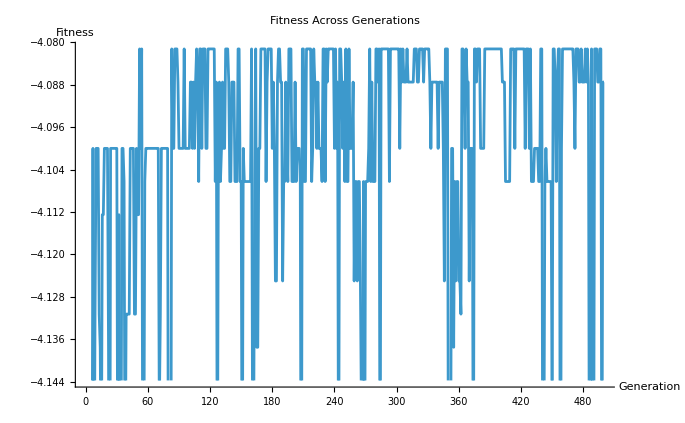

```mathematica
populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}];

fitnessValues={}; (* List to store fitness values *)

Do[
  fitnesses=fitnessFunction /@ population;
  bestFitness=Max[fitnesses];
  bestCandidate=population[[First@Ordering[fitnesses,-1]]];
  AppendTo[fitnessValues,bestFitness];
  parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
  crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
    chars1=Characters[p1];
    chars2=Characters[p2];
    StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
  mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

  children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

  population=children;

,{gen,1,generations}];

bestWord=First@MaximalBy[population,fitnessFunction];
Print[bestWord];
Print[fitnessFunction[bestWord]];

(* Plot the fitness values *)
ListLinePlot[fitnessValues,AxesLabel->{"Generation","Fitness"},PlotLabel->"Fitness Across Generations"]
```